```mathematica
Guy F. Mongelli                                                                                 ECHE 462
Prof. R.M. Sakaran                                                                        3/3/2013
```

```mathematica
Assignment #4
```

```mathematica
Problem#1:
```

```mathematica
At eqilibrium:
```

```mathematica
Solve[Subscript[K, m]==Subscript[c, EZS]/(Subscript[c, S]*Subscript[c, EZ]),Subscript[c, EZ]]
```

{{c_EZ→c_EZS/(c_S K_m)}}

```mathematica
Solve[Subscript[K, i]==Subscript[c, EZI]/(Subscript[c, I]*Subscript[c, EZ]),Subscript[c, EZI]]
```

{{c_EZI→c_ⅈ c_EZ K_i}}

```mathematica
Apply the conservation of enzyme, Ez, such as to write Subscript[c, EZS] in terms of the other expressions:
```

```mathematica
Subscript[c, EZI0]=Subscript[c, EZ]+Subscript[c, EZS]+Subscript[c, EZI]
```

```mathematica
Substitute into the above relation for equilibrium concentrations:
```

```mathematica
Subscript[c, EZI0]=Subscript[c, EZS]/(Subscript[c, S] Subscript[K, m])+Subscript[c, EZS]+Subscript[c, Ι] Subscript[c, EZ] Subscript[K, i]
```

```mathematica
Substitute again for Cez in the third term:
```

```mathematica
Subscript[c, EZI0]=Subscript[c, EZS]/(Subscript[c, S] Subscript[K, m])+Subscript[c, EZS]+Subscript[c, Ι] (Subscript[c, EZS]/(Subscript[c, S] Subscript[K, m])) Subscript[K, i]
```

```mathematica
Solve for Subscript[c, EZS]:
```

```mathematica
Solve[Subscript[c, EZI0]==Subscript[c, EZS]/(Subscript[c, S] Subscript[K, m])+Subscript[c, EZS]+Subscript[c, Ι] (Subscript[c, EZS]/(Subscript[c, S] Subscript[K, m])) Subscript[K, i], Subscript[c, EZS]]
```

{{c_EZS→(c_EZI0 c_S K_m)/(1+c_Ι K_i+c_S K_m)}}

```mathematica
Then, the rate of product formation is:
```

```mathematica
r=Subscript[k, 2] Subscript[c, EZS]
```

```mathematica
r=Subscript[k, 2](Subscript[c, EZI0] Subscript[c, S] Subscript[K, m])/(1+Subscript[c, Ι] Subscript[K, i]+Subscript[c, S] Subscript[K, m])
```

(c_EZI0 c_S k_2 K_m)/(1+c_Ι K_i+c_S K_m)

```mathematica
Solve[(Subscript[c, EZI0] Subscript[c, S] Subscript[k, 2] Subscript[K, m])/(1+Subscript[c, Ι] Subscript[K, i]+Subscript[c, S] Subscript[K, m])==(rmax Subscript[K, m])/(Subscript[K, m](1+Subscript[c, Ι]/Subscript[K, i])+Subscript[c, S]),rmax]
```

{{rmax→(c_EZI0 c_S k_2 (c_S K_i+c_Ι K_m+K_i K_m))/(K_i (1+c_Ι K_i+c_S K_m))}}

```mathematica
FullSimplify[(Subscript[c, EZI0] Subscript[c, S] Subscript[k, 2] (Subscript[c, S] Subscript[K, i]+Subscript[c, Ι] Subscript[K, m]+Subscript[K, i] Subscript[K, m]))/(Subscript[K, i] (1+Subscript[c, Ι] Subscript[K, i]+Subscript[c, S] Subscript[K, m]))]
```

(c_EZI0 c_S k_2 (c_S K_i+(c_Ι+K_i) K_m))/(K_i (1+c_Ι K_i+c_S K_m))

```mathematica
Problem#2:
```

```mathematica
Part A:the PFR case
```

```mathematica
cA0=1.2 (* mol/L *);
```

```mathematica
FA0=10 (* L/min *);
```

```mathematica
VPFR=30 (* L *);
```

```mathematica
The spacetime in mol-min/L is:
```

```mathematica
τ=VPFR/FA0
```

3

```mathematica
∫_0^xA1 1/(0.20(cA0(1-xA))^2)ⅆxA
```

ConditionalExpression[-(5. xA1)/(cA0^2 (-1.+1. xA1)),(Re[xA1]<1.&&Re[xA1]>0&&(Re[1/xA1]>1.||1/xA1∉Reals))||((Re[xA1]<0||xA1∉Reals)&&(Re[1/xA1]≥1.||Re[1/xA1]≤0||1/xA1∉Reals))]

```mathematica
∫_((2-xA)/2)^xA1 1/(0.20(cA0(1-xA))^2)ⅆxA
```

ConditionalExpression[3.47222 (-2./xA+1./(1.-1. xA1)),Re[xA/(-2+xA+2 xA1)]>1||Re[xA/(-2+xA+2 xA1)]<0||xA/(-2+xA+2 xA1)∉Reals]

```mathematica
FullSimplify[(5. (-2./(2.-2. cA0+1. cA0 xA)+1./(1.-1. xA1)))/cA0^2]
```

(-10./(2.-2. cA0+1. cA0 xA)+5./(1.-1. xA1))/cA0^2

```mathematica
Solve[3.4722222222222223 (-2./xA1+1./(1.-1. xA1))==3,xA1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xA1→-3.19641},{xA1→0.724191}}

```mathematica
Solve[τ==∫_0^xA1 1/(0.20(cA0(1-xA))^2)ⅆxA,xA1]
```

{{xA1→0.463519}}

```mathematica
∫_((1+(15/7)(1-xA))/2)^xA1 1/(0.20(cA0(1-xA))^2)ⅆxA
```

ConditionalExpression[3.47222 (-0.933333/(-0.533333+xA)+1./(1.-1. xA1)),Re[(-0.533333+xA)/(-22.+15. xA+14. xA1)]>0.0666667||Re[(-0.533333+xA)/(-22.+15. xA+14. xA1)]<0||(-0.533333+xA)/(-22.+15. xA+14. xA1)∉Reals]

```mathematica
Solve[3.4722222222222223 (-0.9333333333333333/(-0.5333333333333333+xA1)+1./(1.-1. xA1))==3,xA1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xA1→-1.48716},{xA1→0.782835}}

```mathematica
1.2(1-.724)
```

0.3312

```mathematica
1.2(1-.7828)
```

0.26064

```mathematica
(15/7).26
```

0.557143

```mathematica
(cA0/2)(1+(15/7)(1-.7828))
```

0.879257

```mathematica
.26/5
```

0.052

```mathematica
Therefore, the conversion is .463519.
```

```mathematica
Therefore, the concentration of A exiting the PFR in mol/L is:
```

```mathematica
cAout=cA0(1-0.463519)
```

0.643777

```mathematica
Part B: The recycle case
```

```mathematica
Calculate R
```

```mathematica
vr=5 (*L/min*);
```

```mathematica
ve=FA0-vr(*L/min*)
```

5

```mathematica
R=vr/ve
```

1

```mathematica
The lower limit of integration becomes:
```

```mathematica
xi=((R+1)/R)xA1
```

2 xA1

```mathematica
The average inlet concentration which must be used to determine the initial rate:
```

```mathematica
FullSimplify[1-(cA0/(1+R)+(cA0(1-xA)R)/(1+R))/cA0]
```

0.+0.5 xA

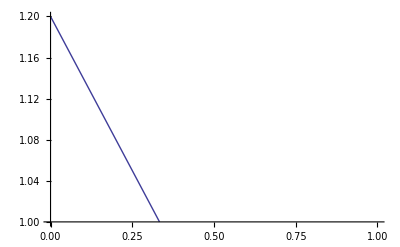

```mathematica
Plot[0.6+0.6 (1-xA),{xA,0,1},PlotRange->{1,1.2}]
```

```mathematica
(R+1)Integrate[1/(0.20((cA0/(1+R)+(cA0(1-xA)R)/(1+R))(1-xA))^2),{xA,0.5*xA1,xA1}]
```

ConditionalExpression[27.7778 ((xA1 (-5.+2. xA1))/(-8.+xA1 (14.+xA1 (-7.+1. xA1)))-2. Log[2.-1. xA1]+2. Log[2.-0.5 xA1]-2. Log[-1.+0.5 xA1]+2. Log[-1.+xA1]),Re[1/xA1]>1.||Re[1/xA1]<0.25||1/xA1∉Reals]

```mathematica
FullSimplify[N[27.77777777777778 ((xA1 (-5.+2. xA1))/(-8.+xA1 (14.+xA1 (-7.+1. xA1)))-2. Log[2.-1. xA1]+2. Log[2.-0.5 xA1]-2. Log[-1.+0.5 xA1]+1.9999999999999996 Log[-1.+xA1]),2]]
```

27.7778 ((xA1 (-5.+2. xA1))/(-8.+xA1 (14.+xA1 (-7.+1. xA1)))-2. Log[2.-1. xA1]+2. Log[2.-0.5 xA1]-2. Log[-1.+0.5 xA1]+2. Log[-1.+xA1])

```mathematica
Solve[τ==27.77 ((xA1 (-5+2 xA1))/(-8+xA1 (14+xA1 (-7+1xA1)))-2Log[2-1 xA1]+2.Log[2.-0.5 xA1]-2. Log[-1.+0.5 xA1]+1.9 Log[-1+xA1]),xA1]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[3==27.77 ((xA1 (-5+2 xA1))/(-8+xA1 (14+(-7+xA1) xA1))-2 Log[2-xA1]+2. Log[2.-0.5 xA1]-2. Log[-1.+0.5 xA1]+1.9 Log[-1+xA1]),xA1]

```mathematica
NSolve[τ==(27.77777777777778 ((-0.16224835026359852+(2.7433725253953978-1.581124175131799 xA1) xA1+(4.000000000000001+xA1 (-6.000000000000002+2.0000000000000004 xA1)) Log[1.-1. xA1]+(-4.000000000000001+(6.000000000000002-2.0000000000000004 xA1) xA1) Log[2.-1. xA1])/(2.+xA1 (-3.+1. xA1))+(-2.3693885222808+xA1 (-1.752209158201534+1.581124175131799 xA1)+(0.888888888888889+(-2.000000000000001-2.0000000000000004 xA1) xA1) Log[-0.19999999999999996+0.6 xA1]+(-0.888888888888889+xA1 (2.000000000000001+2.0000000000000004 xA1)) Log[0.8+0.6 xA1])/(-0.4444444444444444+xA1 (1.0000000000000002+1. xA1)))),xA1]
```

NSolve[3==27.7778 ((-0.162248+(2.74337-1.58112 xA1) xA1+(4.+xA1 (-6.+2. xA1)) Log[1.-1. xA1]+(-4.+(6.-2. xA1) xA1) Log[2.-1. xA1])/(2.+xA1 (-3.+1. xA1))+(-2.36939+xA1 (-1.75221+1.58112 xA1)+(0.888889+(-2.-2. xA1) xA1) Log[-0.2+0.6 xA1]+(-0.888889+xA1 (2.+2. xA1)) Log[0.8+0.6 xA1])/(-0.444444+xA1 (1.+1. xA1))),xA1]

```mathematica
cAout=cA0(1-0.509034)
```

0.589159